## Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(*Some unimportant error messages are sw
itched off for future convenience*)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb,ListInterpolation::inhr];
nbin=1701;
```

## Constants

```mathematica
(* The Subscript[Ω, b] h^2 value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
obh2pl=0.02236;
(* The Subscript[Ω, m] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
ompl=0.3166;
(* The Subscript[H, 0] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
H0pl=67.4; (*67.27*)
(* The dimensionless parameter for the Hubble constant, defined as Subscript[H, 0]/100 *)
h0pl=0.674;
dh0pl=0.005;
(* The h value from Type Ia Supernovae - See abstract of https://arxiv.org/pdf/1903.07603.pdf *)
h0riess=0.7403;
dh0riess=0.0104;
omriess=0.334;
domriess=0.02;
(* CMB temperature *)
Tcmb=2.7255;
(* Various constants useful for the following likelihoods *)
c=299792.458;
cH0=2997.92458;
```

## Equations

```mathematica
(* Define Subscript[z, equality] and Subscript[a, equality] *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
(* E=H/H0 for the transition model *) 
H[a_?NumberQ,om_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))]
```

```mathematica
(*Luminosity Distance*)
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,h_?NumberQ]:=(DLsol[om,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,h]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=((c/(100h))dL[z]/.DLsol[om,h])[[1]]//Chop
```

```mathematica
(*angular diameter distance*)
DA[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=DL[z,om,h]/(1+z)^2
```

```mathematica
Dm3[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=(z+1)*DA[z,om,h]
```

```mathematica
obh2=obh2pl;
ogh2=2.47*10^(-5);
```

```mathematica
R1[a_]:=(3obh2)/(4ogh2*a)
```

```mathematica
cs[a_]:=c/(Sqrt[3(R1[a]+1)])
```

```mathematica
(*transition model*)f1[a_,w0_,wa_,n_]:=(a^(-3*(1+w0+wa)))*(E^(-3*wa*HarmonicNumber[n]+3*a*n*wa*HypergeometricPFQ[{1,1,1-n},{2,2},a]))
```

```mathematica
zeq[om_?NumberQ,h_?NumberQ]:=2.5*(10^4)*om*(h^2)*((Tcmb/2.7)^(-4))
```

```mathematica
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h])
```

```mathematica
(*dimensionless Hubble parameter*)
```

```mathematica
e[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=Sqrt[a^(-3)*om*(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f1[a,w0,wa,n]]
```

```mathematica
(*Sound speed*)
cs[a_?NumberQ,obh2_?NumberQ]:=c/(Sqrt[3(1+(31500 obh2(Tcmb/2.7)^-4)a)] )
```

```mathematica
(*redshift at decupling A. Theodoropoulos page 37, eq 2.42*)
g1[obh2_?NumberQ]:=(0.0783*(obh2)^(-0.238))/(1+39.5*(obh2)^(0.763));
g2[obh2_?NumberQ]:=0.560/(1+21.1*(obh2)^(1.81));
zdec[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^(-0.738))*(1+g1[obh2]*(om*(h^2))^(g2[obh2]));

(*comoving sound horizon*)
rs[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[x,obh2]/((x^2)*100h*e[x,om,w0,wa,n,h]),{x,0,1/(1+ze)}]
```

```mathematica
(*comoving sound horizon at decoupling*)
rsdec[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[a,obh2]/((a^2)*100h*e[a,om,w0,wa,n,h]),{a,0,1/(1+zdec[om,obh2,h])}]
```

```mathematica
hz[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h*e[1/(1+z),om,w0,wa,n,h]
```

```mathematica
(*luminosity distance*)
```

```mathematica
Clear[DLsol1,DL1,dL1]
DLsol1[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsol1[om,w0,wa,n,h]=NDSolve[{D[dL1[zz]/(1+zz),zz]==1/(h*100*e[1/(1+zz),om,w0,wa,n,h]/(100h)),dL1[0]==0},dL1,{zz,0,1300},MaxSteps->Infinity])
DL1[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((c/(100h))dL1[z]/.DLsol1[om,w0,wa,n,h])[[1]]//Chop
```

```mathematica
(*angular diameter distance*)
DA1[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=DL1[z,om,w0,wa,n,h]/(1+z)^2
```

```mathematica
(*comoving angular distance at decoupling*)
Dm1[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(c/(100*h))*NIntegrate[(hz[z,om,w0,wa,n,h]/100h)^(-1),{z,0,zdec[om,obh2,h]}];
Dm2[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(zdec[om,obh2,h]+1)*DA1[zdec[om,obh2,h],om,w0,wa,n,h];
Dm4[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(z+1)*DA1[z,om,w0,wa,n,h]
```

```mathematica
Dv[z_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((c*z*((1+z)^2)*(DA[z,om,w0,wa,n,h]^2))/hz[z,om,w0,wa,n,h])^(1/3)
```

```mathematica
(*BAO dz ratio =rs/Dv*)
dz[z_,om_,obh2_,w0_,wa_,n_,h_]:=rs[zdec[om,obh2,h],om,obh2,w0,wa,n,h]/Dv[z,om,w0,wa,n,h]
```

```mathematica
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=c/hz[z,om,w0,wa,n,h]
```

```mathematica
(*CMB shift parameter*)
R[om_,obh2_,w0_,wa_,n_,h_]:=(Sqrt[om (100h)^2]*Dm2[om,obh2,w0,wa,n,h])/c
```

```mathematica
(* Drag redshift: https://arxiv.org/pdf/astro-ph/9709112.pdf eq 4 page 5*)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om*h^2)^0.251)/(1+0.659 (om*h^2)^0.828)(1+(0.313(om*h^2)^-0.419(1+0.607(om*h^2)^0.674))(obh2)^(0.238(om*h^2)^0.223))
```

```mathematica
la[om_,obh2_,w0_,wa_,n_,h_]:=(Pi*Dm2[om,obh2,w0,wa,n,h])/rsdec[om,obh2,w0,wa,n,h]
```

## Pantheon+ Data

```mathematica
dataPanth=Import[".\\data\\lcparam_full_long_zhel-pp.txt","Table"];
(* Length of Pantheon data *)
ndatPanth=Length[dataPanth]-1;
```

```mathematica
(* Isolate the relevant part of the Pantheon+ data: z, mb, dmb, mu=mb-M, dmu, muceph, iscamibrator(1,0) , in a short version of the Pantheon+ data. *)
tabdat=Table[{dataPanth[[1+i,3]],dataPanth[[1+i,9]],dataPanth[[1+i,10]],dataPanth[[1+i,11]],dataPanth[[1+i,12]],dataPanth[[1+i,13]],dataPanth[[1+i,14]]},{i,1,ndatPanth}];
tabdat1=Table[{dataPanth[[1+i,3]],dataPanth[[1+i,11]],dataPanth[[1+i,12]]},{i,1,ndatPanth}];
```

```mathematica
(*Assuming tabdat1 is already defined and contains 1701 data points*)(*Determine the number of data points per bin for the first nbin bins*)
numDataPoints=Length[tabdat1];
binSize=Floor[numDataPoints/nbin];(*Use Floor instead of Ceiling to have nbin equal bins*)
```

```mathematica
(*Sort the data by redshift*)
sortedData=SortBy[tabdat1,First];
```

```mathematica
(*Function to calculate the mean z,weighted mean of μ and uncertainty dμ for each bin*)
meanFunction[bin_]:=Module[{zs,mus,dmus},zs=bin[[All,1]];
mus=bin[[All,2]];
dmus=bin[[All,3]];
(*Weighted mean of μ*)weightedMean=Total[mus/dmus^2]/Total[1/dmus^2];
(*Combined uncertainty of μ*)combinedUncertainty=Sqrt[1/Total[1/dmus^2]];
(*Mean redshift*)meanZ=Mean[zs];
{meanZ,weightedMean,combinedUncertainty}]
```

```mathematica
(*Bin the data and calculate the mean for each bin containing n=binSize elements*)
tabdatbinned=Table[meanFunction[sortedData[[((i-1)*binSize+1);;(i*binSize)]]],{i,1,nbin-1}];
(*The last bin gets the remaining data points*)
lastBin=sortedData[[((nbin-1)*binSize+1);;]];
lastBinMean=meanFunction[lastBin];
tabdatbinned=Append[tabdatbinned,lastBinMean];
```

```mathematica
(*meanFunction was applied for groups of n=binSize elements, nbin=100 times and so we have ~100 results in one 3x100 matrix*)
```

```mathematica
(*mean z, weighted mean mu, combined uncertainty*)(*MatrixForm[tabdatbinned]*)
```

## Bao Data

### Constants and Equations

```mathematica
(*Planck 2018 ΛCDM model parameters*)

H0=67.4;(*Hubble constant in km/s/Mpc*)

Ωm=0.315;(*Matter density parameter*)

ΩΛ=0.685;(*Dark energy density parameter*)

Ωr=9.26*10^-5;(*Radiation density parameter including CMB and relativistic neutrinos*)

(*Sound horizon at the drag epoch rd in Mpc,from Planck 2018*)rd=147.18;
```

```mathematica
(*Function to calculate the comoving angular diameter distance DM(z)*)
DM[z_?NumericQ]:=NIntegrate[c/(H0 Sqrt[Ωm (1+zp)^3+ΩΛ+Ωr (1+zp)^4]),{zp,0,z}]
```

## New binnging for contours (BAO)

```mathematica
Allbao=SortBy[{(*{0.38,10.27,0.15},*){0.51,13.38,0.18},(*{0.7,17.48,0.23},*)(*{0.7,17.65,0.3},*){0.7,17.96,0.51},{0.77,18.85,0.38},(*{0.835,18.92,0.51},*){0.835,19.15,0.58}(*,{0.845,18.90,0.78}*)(*,{0.845,19.84,0.53}*),{0.85,19.5,1},{1.48,30.21,0.79},{2.33,37.5,1.1},(*{0.11,1.95,0.10},*){0.7,17.28,0.89},{0.87,21.39,1.39},{1.00,23.13,2.07},{2.00,36.18,1.69},{2.35,36.3,1.8},{2.40,36.6,1.2},{2.34,37.72,2.18},(*{2.36,36.29,1.34},*){0.38,10.27,0.15},(*{0.51,13.38,0.18},*){0.61,15.45,0.22},{0.81,19.46,0.78},(*{2.40,36.6,1.2},*){0.32,8.76,0.14},{0.44,11.79,1.11},(*{0.51,11.92,0.18},*){0.54,14.76,0.68},{0.6,14.99,1.04},{0.73,18.03,1.26}(*,{2.34,37.68,2.17},{2.36,36.29,1.34}*),{0.51,13.62,0.25},{0.71,16.85,0.32},{0.93,21.71,0.28},{1.32,27.79,0.69},{2.33,39.71,0.94},{0.59,15.29,0.25},{0.32,8.54,0.25},{0.8,19.54,2.07},{1.5,30.51,1.85},{2.2,38.09,1.73}},First]
```

{{0.32,8.54,0.25},{0.32,8.76,0.14},{0.38,10.27,0.15},{0.44,11.79,1.11},{0.51,13.38,0.18},{0.51,13.62,0.25},{0.54,14.76,0.68},{0.59,15.29,0.25},{0.6,14.99,1.04},{0.61,15.45,0.22},{0.7,17.28,0.89},{0.7,17.96,0.51},{0.71,16.85,0.32},{0.73,18.03,1.26},{0.77,18.85,0.38},{0.8,19.54,2.07},{0.81,19.46,0.78},{0.835,19.15,0.58},{0.85,19.5,1},{0.87,21.39,1.39},{0.93,21.71,0.28},{1.,23.13,2.07},{1.32,27.79,0.69},{1.48,30.21,0.79},{1.5,30.51,1.85},{2.,36.18,1.69},{2.2,38.09,1.73},{2.33,37.5,1.1},{2.33,39.71,0.94},{2.34,37.72,2.18},{2.35,36.3,1.8},{2.4,36.6,1.2}}

### Bins

```mathematica
baobin1=Table[{If[Allbao[[i,1]]<0.3,Allbao[[i,1]],0],Allbao[[i,2]],Allbao[[i,3]]},{i,1,Length[Allbao]}];
```

```mathematica
baobin2=Table[{If[0.3<Allbao[[i,1]]<0.5,Allbao[[i,1]],0],Allbao[[i,2]],Allbao[[i,3]]},{i,1,Length[Allbao]}];
```

```mathematica
baobin3=Table[{If[Allbao[[i,1]]<0.8,Allbao[[i,1]],0],Allbao[[i,2]],Allbao[[i,3]]},{i,1,Length[Allbao]}];
```

```mathematica
baobin4=Table[{If[0.8<Allbao[[i,1]]<2.5,Allbao[[i,1]],0],Allbao[[i,2]],Allbao[[i,3]]},{i,1,Length[Allbao]}];
```

```mathematica
baobin5=Table[{If[0.8<Allbao[[i,1]]<2.5,Allbao[[i,1]],0],Allbao[[i,2]],Allbao[[i,3]]},{i,1,Length[Allbao]}];
```

### X^2

```mathematica
X2bao3[om_?NumberQ,h_?NumberQ]:=Sum[(Allbao[[i,2]]-(Dm3[Allbao[[i,1]],om,h]/147.18(*rd*)))^2/(Allbao[[i,3]]^2+(0.29(*rd σ*))^2),{i,1,15}]
minBao3=FindMinimum[X2bao3[om,h],{om,0.28},{h,0.65}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{6.38323,{om→0.313657,h→0.681568}}

```mathematica
X2bao4[om_?NumberQ,h_?NumberQ]:=Sum[(Allbao[[i,2]]-(Dm3[Allbao[[i,1]],om,h]/147.18(*rd*)))^2/(Allbao[[i,3]]^2+(0.29)^2),{i,16,32}]
minBao4=FindMinimum[X2bao4[om,h],{om,0.28},{h,0.65}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{10.8723,{om→0.346109,h→0.672512}}

```mathematica
omBAO3=minBao3[[2,1,2]];
hBAO3=minBao3[[2,2,2]];
omBAO4=minBao4[[2,1,2]];
hBAO4=minBao4[[2,2,2]];
```

### Errors

```mathematica
dX[nsig_,M_]:=2*InverseGammaRegularized[M/2,1-Erf[nsig/(Sqrt[2])]]//N;
```

```mathematica
paramsBao={om,h};
```

```mathematica
chifunBao3=ListInterpolation[ParallelTable[X2bao3[om,h],{om,omBAO3-0.05,omBAO3+0.05,0.02},{h,hBAO3-0.05,hBAO3+0.05,0.02},DistributedContexts->Automatic],{{omBAO3-0.05,omBAO3+0.05},{hBAO3-0.05,hBAO3+0.05}}];
FijBao3=0.5*Table[D[chifunBao3[om,h],paramsBao[[p]],paramsBao[[d]]]/.minBao3[[2]],{p,1,Length[paramsBao]},{d,1,Length[paramsBao]}];
cijBao3=Inverse[FijBao3];
errorsBao3=Sqrt[Diagonal[cijBao3]]
```

{0.100323,0.0266649}

```mathematica
chifunBao4=ListInterpolation[ParallelTable[X2bao4[om,h],{om,omBAO4-0.05,omBAO4+0.05,0.02},{h,hBAO4-0.05,hBAO4+0.05,0.002},DistributedContexts->Automatic],{{omBAO4-0.05,omBAO4+0.05},{hBAO4-0.05,hBAO4+0.05}}];
FijBao4=0.5*Table[D[chifunBao4[om,h],paramsBao[[p]],paramsBao[[d]]]/.minBao4[[2]],{p,1,Length[paramsBao]},{d,1,Length[paramsBao]}];
cijBao4=Inverse[FijBao4];
errorsBao4=Sqrt[Diagonal[cijBao4]]
```

{0.0592788,0.0270454}

### Sigma distance

```mathematica
sigma34h=(Abs[hBAO4-hBAO3])/(Sqrt[(errorsBao4[[2]]^2)+(errorsBao3[[2]]^2)])
```

0.238465

```mathematica
sigma34om=(Abs[omBAO4-omBAO3])/(Sqrt[(errorsBao4[[1]]^2)+(errorsBao3[[1]]^2)])
```

0.278485

### Contours

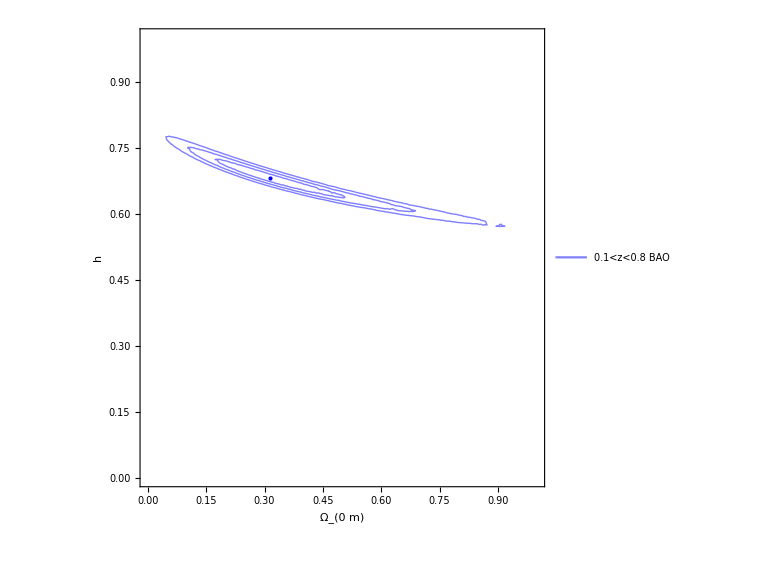

```mathematica
contourbao3=ContourPlot[X2bao3[om,h],{om,0,1},{h,0,1},Contours->{minBao3[[1]]+dX[1,2],minBao3[[1]]+dX[2,2],minBao3[[1]]+dX[3,2]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Blue,Point[{omBAO3,hBAO3}]}},ContourShading->False,ContourStyle->Blue,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"0.1<z<0.8 BAO"},{0.6,0.9}]]
```

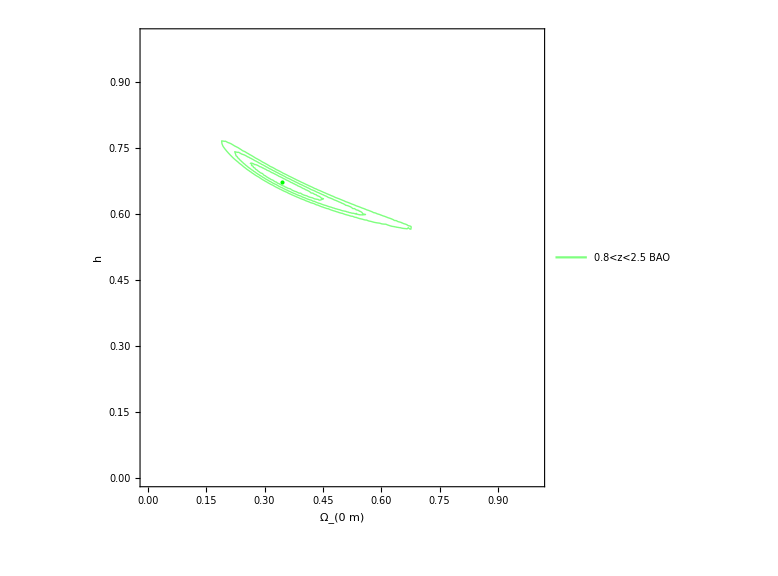

```mathematica
contourbao4=ContourPlot[X2bao4[om,h],{om,0,1},{h,0,1},Contours->{minBao4[[1]]+dX[1,2],minBao4[[1]]+dX[2,2],minBao4[[1]]+dX[3,2]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Green,Point[{omBAO4,hBAO4}]}},ContourShading->False,ContourStyle->Green,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"0.8<z<2.5 BAO"},{0.6,0.8}]]
```

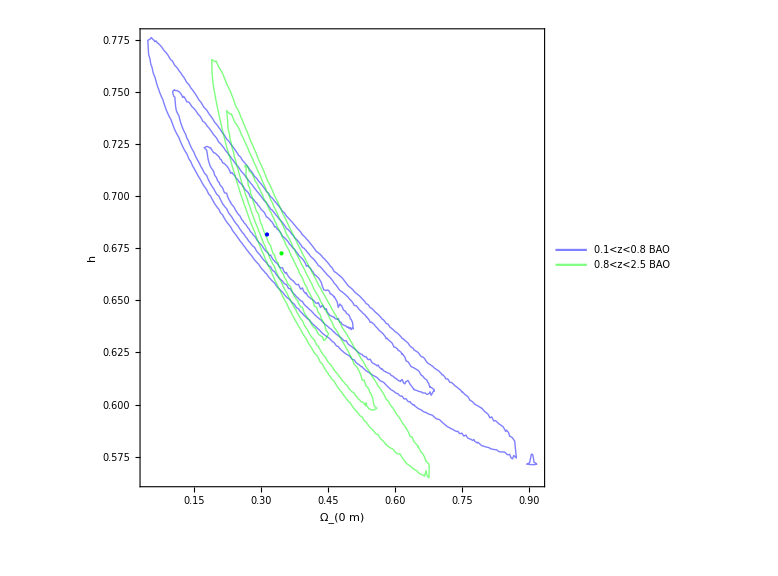

```mathematica
ContourPlotbao1=Show[contourbao3,contourbao4,PlotRange->{All,All},Epilog->{{PointSize[Large],Blue,Point[{omBAO3,hBAO3}]},{PointSize[Large],Green,Point[{omBAO4,hBAO4}]}}]
```

```mathematica
(*must have contourBAOnew from fig4 eveluated first*)
```

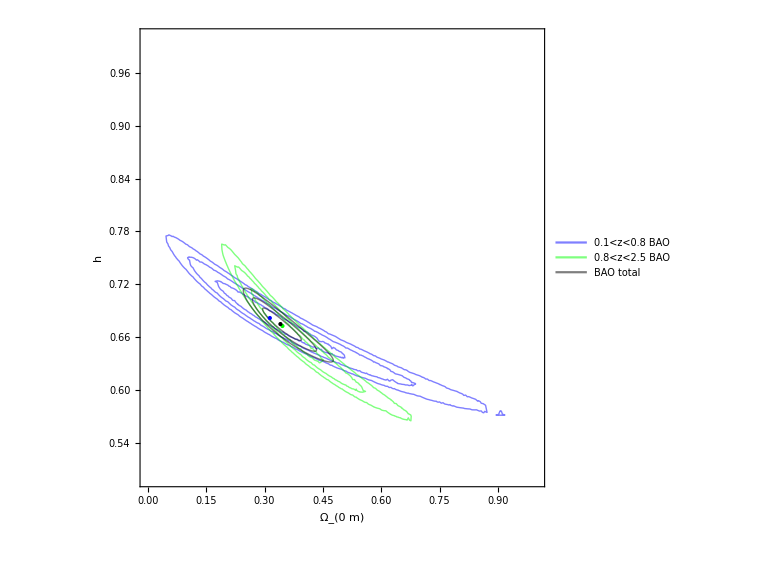

```mathematica
ContourPlotbao2=Show[contourbao3,contourbao4,contourBAOnew ,PlotRange->{{0,1},{0.5,1}},Epilog->{{PointSize[Large],Blue,Point[{omBAO3,hBAO3}]},{PointSize[Large],Green,Point[{omBAO4,hBAO4}]},{PointSize[Large],Black,Point[{omBaonew,hBaonew}]}}]
```

## New binning for contours (Pan+)

### Bins

```mathematica
newbin1=Table[{If[tabdat[[i,1]]<0.1,tabdat[[i,1]],0],If[tabdat[[i,1]]<0.1,tabdat[[i,2]],0],If[tabdat[[i,1]]<0.1,tabdat[[i,3]],0],tabdat[[i,6]],tabdat[[i,7]],tabdat[[i,4]]},{i,1,Length[tabdat]}];
```

```mathematica
newbin2=Table[{If[tabdat[[i,1]]<0.2,tabdat[[i,1]],0],If[tabdat[[i,1]]<0.2,tabdat[[i,2]],0],If[tabdat[[i,1]]<0.2,tabdat[[i,3]],0],tabdat[[i,6]],tabdat[[i,7]],tabdat[[i,4]]},{i,1,Length[tabMu]}];


newbin5=Table[{If[0.1<tabdat[[i,1]]<0.3,tabdat[[i,1]],0],If[tabdat[[i,1]]<0.5,tabdat[[i,2]],0],If[tabdat[[i,1]]<0.5,tabdat[[i,3]],0],tabdat[[i,6]],tabdat[[i,7]],tabdat[[i,4]]},{i,1,Length[tabdat]}];



newbin10=Table[{If[0.3<tabdat[[i,1]]<0.5,tabdat[[i,1]],0],If[tabdat[[i,1]]<1.0,tabdat[[i,2]],0],If[tabdat[[i,1]]<1.0,tabdat[[i,3]],0],tabdat[[i,6]],tabdat[[i,7]],tabdat[[i,4]]},{i,1,Length[tabdat]}];
```

```mathematica
newbin15=Table[{If[0.1<tabdat[[i,1]]<0.8,tabdat[[i,1]],0],If[tabdat[[i,1]]<1.5,tabdat[[i,2]],0],If[tabdat[[i,1]]<1.5,tabdat[[i,3]],0],tabdat[[i,6]],tabdat[[i,7]],tabdat[[i,4]]},{i,1,Length[tabdat]}];
```

```mathematica
Count[bin27m,_-0]


newbin23=Table[{If[0.8<tabdat[[i,1]]<2.3,tabdat[[i,1]],0],If[tabdat[[i,1]]<2.3,tabdat[[i,2]],0],If[tabdat[[i,1]]<2.3,tabdat[[i,3]],0],tabdat[[i,6]],tabdat[[i,7]],tabdat[[i,4]]},{i,1,Length[tabdat]}];
```

1701

### X^2

```mathematica
newchi15[M_,om_,h_]:=Module[{Δm15},Δm15=Table[If[newbin15[[i,1]]≠0,If[newbin15[[i,5]]==1,newbin15[[i,2]]-M -newbin15[[i,6]],newbin15[[i,2]]-(M+5 Log10[DL[newbin15[[i,1]],om,h]]+25)],0],{i,1,Length[newbin15]}];Δm15.InvCov.Δm15]
newmin15=FindMinimum[newchi15[M,om,h],{M,-19.2},{om,0.3},{h,0.7}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{808.991,{M→-19.2133,om→0.365107,h→0.742179}}

```mathematica
newchi23[M_,om_,h_]:=Module[{Δm23},Δm23=Table[If[newbin23[[i,1]]≠0,If[newbin23[[i,5]]==1,newbin23[[i,2]]-M -newbin23[[i,6]],newbin23[[i,2]]-(M+5 Log10[DL[newbin23[[i,1]],om,h]]+25)],0],{i,1,Length[newbin23]}];Δm23.InvCov.Δm23]
newmin23=FindMinimum[newchi23[M,om,h],{M,-19.2},{om,0.3},{h,0.7}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{25.9037,{M→-19.2021,om→0.377417,h→0.706798}}

```mathematica
MP15=newmin15[[2,1,2]];
omP15=newmin15[[2,2,2]];
hP15=newmin15[[2,3,2]];
```

```mathematica
MP23=newmin23[[2,1,2]];
omP23=newmin23[[2,2,2]];
hP23=newmin23[[2,3,2]];
```

```mathematica
dX[1,3]
```

3.52674

### Contours

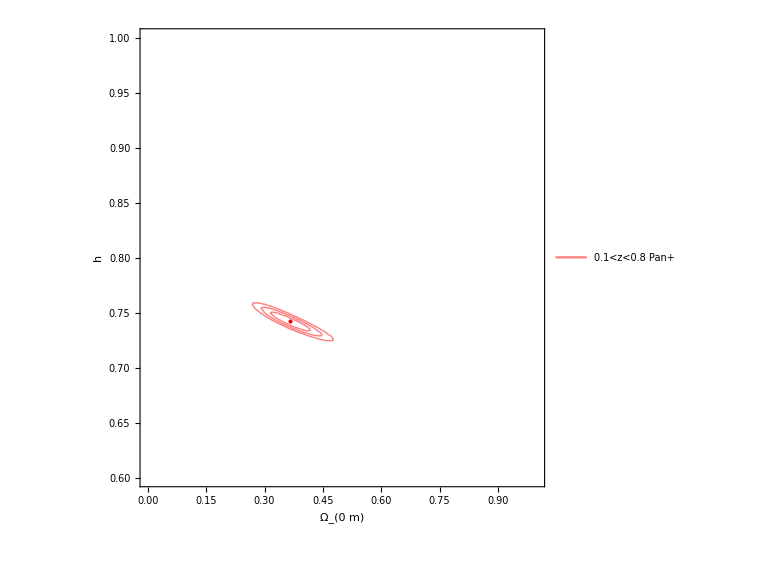

```mathematica
contour6=ContourPlot[newchi15[MP15,om,h],{om,0,1},{h,0.6,1},Contours->{newmin15[[1]]+dX[1,3],newmin15[[1]]+dX[2,3],newmin15[[1]]+dX[3,3]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Red,Point[{omP15,hP15}]}},ContourShading->False,ContourStyle->Red,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"0.1<z<0.8 Pan+"},{0.6,0.8}]]
```

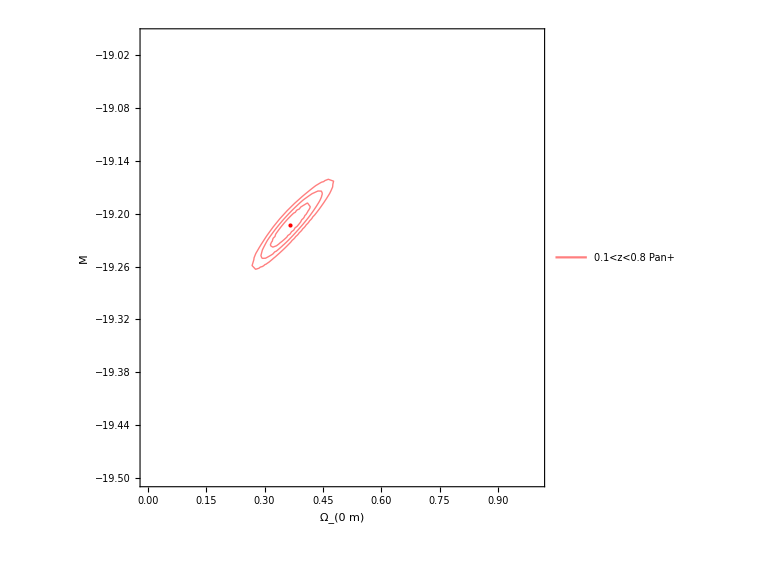

```mathematica
contour65=ContourPlot[newchi15[M,om,hP15],{om,0,1},{M,-19,-19.5},Contours->{newmin15[[1]]+dX[1,3],newmin15[[1]]+dX[2,3],newmin15[[1]]+dX[3,3]},FrameLabel->{"Ω_(0  m)","M"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Red,Point[{omP15,MP15}]}},ContourShading->False,ContourStyle->Red,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"0.1<z<0.8 Pan+"},{0.6,0.8}]]
```

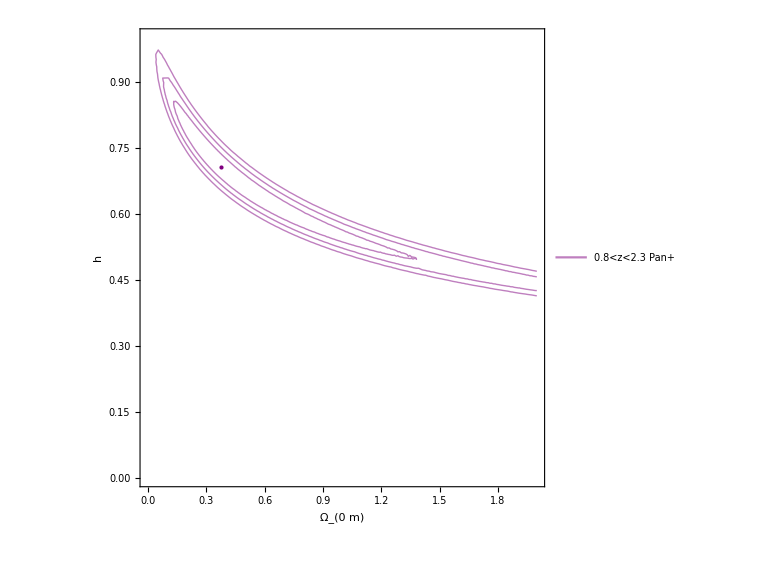

```mathematica
contour7=ContourPlot[newchi23[MP23,om,h],{om,0,2},{h,0,1},Contours->{newmin23[[1]]+dX[1,3],newmin23[[1]]+dX[2,3],newmin23[[1]]+dX[3,3]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Purple,Point[{omP23,hP23}]}},ContourShading->False,ContourStyle->Purple,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"0.8<z<2.3 Pan+"},{0.6,0.7}]]
```

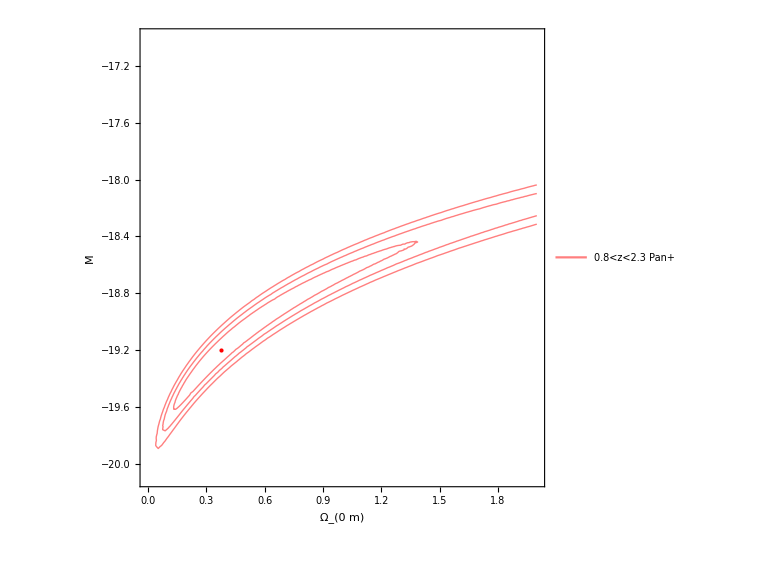

```mathematica
contour75=ContourPlot[newchi23[M,om,hP23],{om,0,2},{M,-17,-20.1},Contours->{newmin23[[1]]+dX[1,3],newmin23[[1]]+dX[2,3],newmin23[[1]]+dX[3,3]},FrameLabel->{"Ω_(0  m)","M"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Red,Point[{omP23,MP23}]}},ContourShading->False,ContourStyle->Red,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"0.8<z<2.3 Pan+"},{0.6,0.8}]]
```

```mathematica
(*Must have contour2 from fig4 evaluated first*)
```

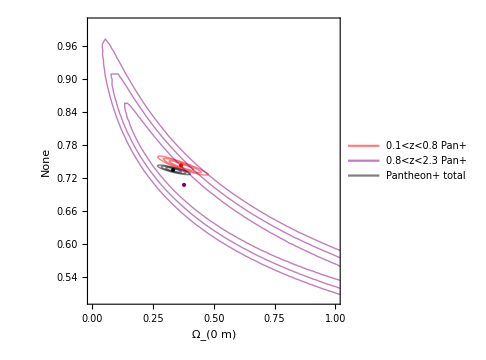

```mathematica
ContourPlot3=Show[contour6,contour7,contour2,PlotRange->{{0,1},{0.5,1}},Frame->{{False,True},{True,True}},FrameLabel->{"Ω_(0  m)","None"},Epilog->{{PointSize[Large],Purple,Point[{omP23,hP23}]},{PointSize[Large],Red,Point[{omP15,hP15}]},{PointSize[Large],Black,Point[{omP,hP}]}},ImageSize->Medium]
```

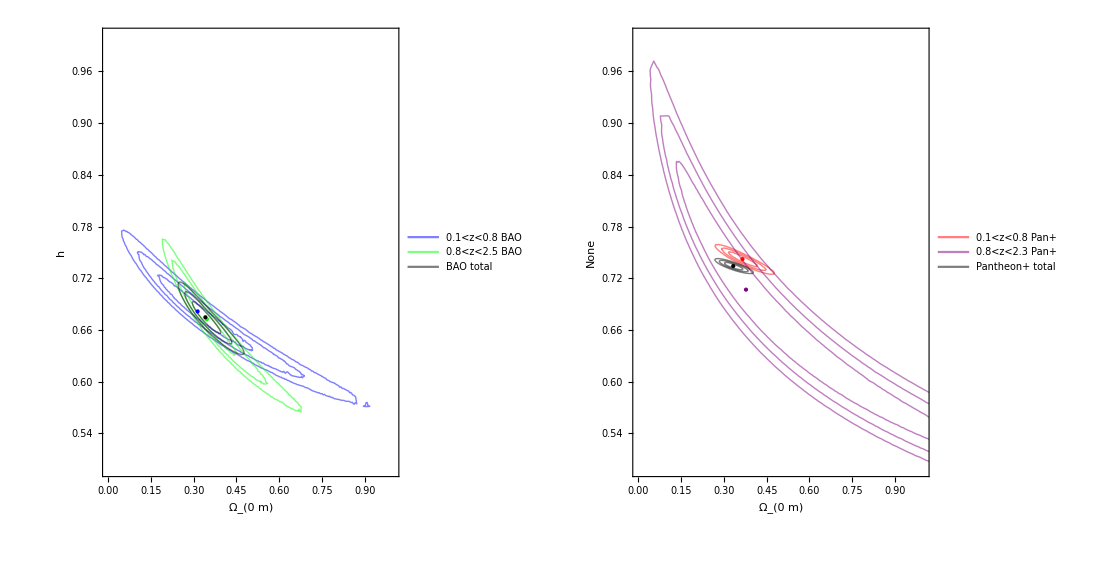

```mathematica
GraphicsGrid[{{ContourPlotbao2,ContourPlot3}},Spacings->-40,ImageSize->1100]
```

## BAO + Pan+ contours

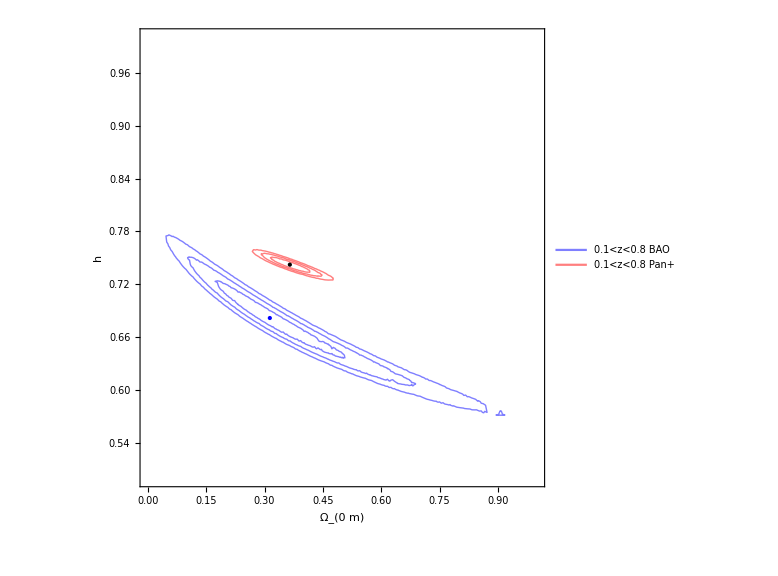

```mathematica
ContourPlot3tot=Show[contourbao3,contour6,PlotRange->{{0,1},{0.5,1}},Epilog->{{PointSize[Large],Blue,Point[{omBAO3,hBAO3}]},{PointSize[Large],Black,Point[{omP15,hP15}]}}]
```

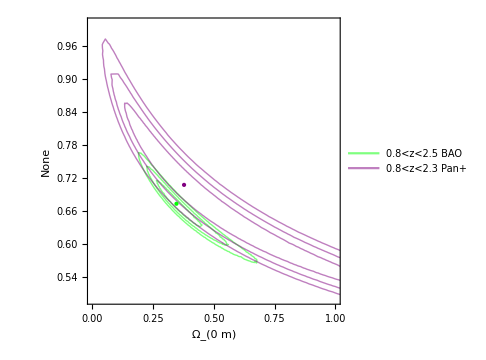

```mathematica
ContourPlot4tot=Show[contourbao4,contour7,PlotRange->{{0,1},{0.5,1}},Frame->{{False,True},{True,True}},FrameLabel->{"Ω_(0  m)","None"},Epilog->{{PointSize[Large],Green,Point[{omBAO4,hBAO4}]},{PointSize[Large],Purple,Point[{omP23,hP23}]}},ImageSize->Medium]
```

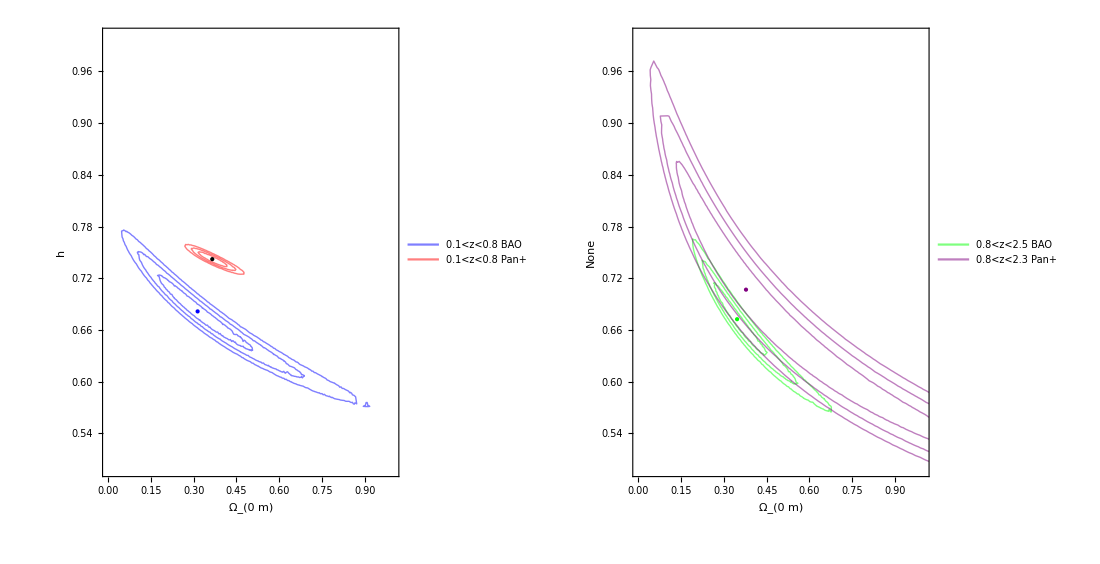

-Graphics-

```mathematica
GraphicsGrid[{{ContourPlot3tot,ContourPlot4tot}},Spacings->-40,ImageSize->1100]
```